## Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
readStanDataset[filename_]:=Module[{rawD},
	rawD=Import[filename]//Select[NumberQ[#[[1]]]||StringTake[#[[1]],1]!="#"&];
	Dataset[AssociationThread[rawD[[1]],#]&/@Rest[rawD]]
]
```

```mathematica
paramInEllipsoidQ[θ_, θStar_, cov_] := Module[{x, invMat},
	x = θ - θStar;
	invMat = Inverse[cov];
	x.invMat.x < 1
]
```

```mathematica
(*This is from Reichl et al 2020. Adapted using MatrixPower[#, 1/2] to give correct results.*)
getEllDraw[θStar_, cov_] := Module[
	{k, rs, pt, λs, λh, eVals, eVecs},
	k = Length@cov;
	rs = RandomVariate[UniformDistribution[]];
	pt = RandomVariate[NormalDistribution[], k];
	λs = Total[pt^2];
	λh = rs^(1/k)/√λs;
	eVals = Eigenvalues[MatrixPower[cov, 1/2]];
	eVecs = Eigenvectors[MatrixPower[cov, 1/2]];
	(λh pt eVals).eVecs + θStar
]
```

```mathematica
(*This is from Reichl et al. 2020*)
getEllipsoidVolume[mat_] := Module[
	{k = Length@mat, v, e, i},
	v = Table[0, k+1];
	e = Eigenvalues@mat;
	v[[1]] = Log[1];
	v[[2]] = Log[2];
	For[i=3, i<=k+1, i++, v[[i]] = Log[(2Pi)/(i - 1)] + v[[i-2]]];
	v[[k+1]] + Total[Log@Sqrt[e]]
]
```

```mathematica
(*The following is from Reichl 2020 Appendix A.3*)
getAlpha[posteriorDraws_, unnormalisedLoglValues_, θStar_, d_]:=Module[
	{lP, l, ρ, lpHigh, logLValues, lpLow, αLow=0.01, αHigh=100.0, α, αMax, αMin, c, δA, zip},
	l = Length@posteriorDraws;
	ρ = Median[unnormalisedLoglValues];
	lP = 0.49l;
	αMax = αHigh;
	αMin = αLow;
	δA = αHigh - αLow;
	c = 0;
	While[δA > 0.1,
		δA = αHigh - αLow;
		{lpLow, lpHigh} = Table[
			zip = Transpose[{posteriorDraws, unnormalisedLoglValues}];
			Length[Select[zip, paramInEllipsoidQ[#[[1]], θStar, α d] && #[[2]] > ρ &]],
			{α, {αLow, αHigh}}
		];
		If[lpHigh > lP,
			If[c==0, αMax = Max[αHigh, αMax], If[αHigh<αMax, αMax=αHigh]];
			αHigh=(αLow+αHigh)/2;
			c=1;,
			If[c==1, αHigh=Min[αHigh+10,αMax], αHigh=αHigh+100]
		];
		If[lpLow<lP,
			If[αLow>αMin,αMin==αLow];
			αLow=(αLow+αHigh)/2;,
			αLow=Max[(1+αLow)/2,αMin];
		]
	];
	αHigh
]
```

```mathematica
logMarginalLikelihood[posteriorDraws_,loglValues_,logLfunc_] := Module[
	{ρ, d, maxLogl, maxIndex, θStar,α,ellDraws,piHat,logIntegrationVolume,logκ},
	ρ=Median@loglValues;
	d=Covariance@posteriorDraws;
	maxLogl=Max@loglValues;
	maxIndex=Ordering[loglValues,-1]//First;
	θStar=posteriorDraws[[maxIndex]];
	α=getAlpha[posteriorDraws,loglValues,θStar,d];
	Print["Estimating α as ", α];
	ellDraws=Table[getEllDraw[θStar,α d],1000];
	piHat=N[Length@Select[ellDraws,logLfunc[#]>ρ&]/Length@ellDraws];
	Print["Estimating piHat as ", piHat];
	logIntegrationVolume=getEllipsoidVolume[α d]+Log[piHat];
	logκ=Log[Mean[
		MapThread[
			If[paramInEllipsoidQ[#1,θStar,α d]&&#2>ρ,1/Exp[#2-ρ],0]&,
			{posteriorDraws,loglValues}
		]
	]] - ρ;
	logIntegrationVolume - logκ
]
```

## Tests

### Ellipsoid Sampling tests

Let’s define an arbitrary two-dimensional covariance matrix, and a mid-point of (0.5, 0.5):

```mathematica
θStar={0.5,0.5};cov={{0.1,0.08},{0.08,0.2}};
MatrixForm[cov]
```

(0.1 | 0.08
0.08 | 0.2)

Sampling within and coloring using the paramInEllipsoidQ function:

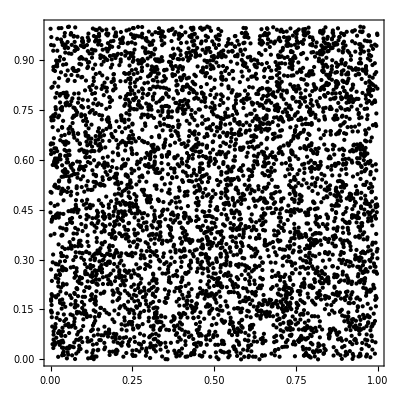

```mathematica
randomPoints=RandomVariate[UniformDistribution[10000]]//Partition[#,2]&;
colors=Table[If[paramInEllipsoidQ[p,θStar,cov],Red,Blue],{p,randomPoints}];
Graphics[
Point[randomPoints,VertexColors->colors],AspectRatio->1,ImagePadding->20,Frame->True]
```

Now performing random sampling using getEllDraw and overlaying with the above sampled points:

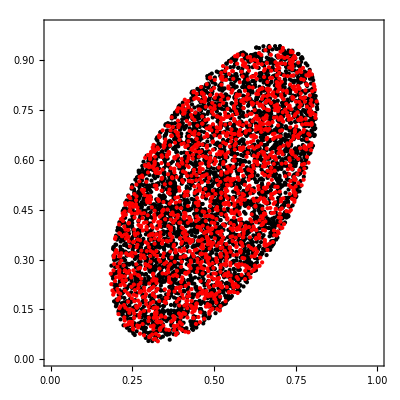

```mathematica
randomPoints2=Table[getEllDraw[θStar,cov],4000];
Graphics[
{
Black,Point[randomPoints2],
Red,Point[Select[randomPoints,paramInEllipsoidQ[#,θStar,cov]&]]
},
AspectRatio->1,ImagePadding->20,Frame->True,PlotRange->{{0,1},{0,1}}
]
```

Looks right, but I had to tweak the original function from Reichl. et al to take the “Square root” of the matrix first, see above.

### Ellipsoid Volume test

```mathematica
dimensions={1,2,3,4};
radii={1,2,3,4};
TableForm[
Table[
{
d,
Exp[getEllipsoidVolume[IdentityMatrix[d]]],
Exp[getEllipsoidVolume[DiagonalMatrix[radii[[;;d]]]]],
Exp[getEllipsoidVolume[2^2 IdentityMatrix[d]]]
},
{d,dimensions}
],
TableHeadings->{None, {"Dimension","Volume Unit Sphere", "Volume Ellipsoid","Volume twice Unit Sphere"}}
]
```

Dimension | Volume Unit Sphere | Volume Ellipsoid | Volume twice Unit Sphere
1 | 2 | 2 | 4
2 | π | √2 π | 4 π
3 | (4 π)/3 | 4 √(2/3) π | (32 π)/3
4 | π^2/2 | √6 π^2 | 8 π^2

This looks right. It seems the input matrix must be in the form of a covariance matrix, where the radii are considered squared

### Simple two-dimensional case study

We consider a two-dimensional parameter space with flat priors from 0 to 1:

```mathematica
priorDist=ProductDistribution[
UniformDistribution[],
UniformDistribution[]
];
```

And a posterior as a Normal distribution centered in the middle:

```mathematica
posteriorDist=MultinormalDistribution[{0.5,0.5},{{0.002,0.002},{0.002,0.006}}];
```

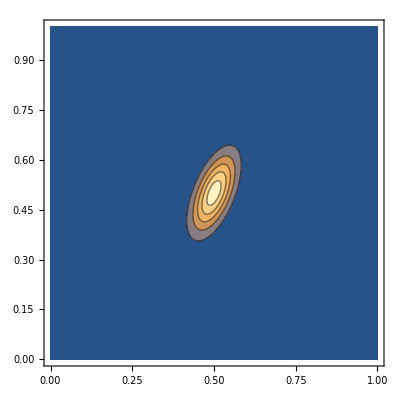

```mathematica
ContourPlot[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All]
```

We define a fake unnormalised likelihood function with a fake normalisation constant of 10^-6:

```mathematica
logLfunc[θ_]:=Log[10^-6]+LogLikelihood[posteriorDist,{θ}]
```

#### Naive computation using prior draws

We can first use the naive marginal likelihood estimator using prior draws:

```mathematica
priorDraws=RandomVariate[priorDist,10000];
loglValues=logLfunc/@priorDraws;
```

with a maximum of

```mathematica
scale=Max[loglValues]
```

-9.78622

which we use to scale and compute the log-evidence as mean of the loglValues on the prior draws:

```mathematica
Log[Mean[Exp[loglValues-scale]]]+scale
```

-13.7577

which is pretty close to our theoretical value of

```mathematica
N@Log[10^-6]
```

-13.8155

#### Reichl 2020 Method

We first create fake draws from the posterior, mimicking an MCMC outcome:

```mathematica
posteriorDraws=RandomVariate[posteriorDist,2000];
```

and compute the unnormalised likelihood values for it:

```mathematica
loglValues=logLfunc/@posteriorDraws;
```

and set up the necessary quantities:

```mathematica
ρ=Median@loglValues
d=Covariance@posteriorDraws
maxLogl=Max@loglValues
maxIndex=Ordering[loglValues,-1]//First
θStar=posteriorDraws[[maxIndex]]
```

-10.4634

{{0.00199751,0.00186824},{0.00186824,0.00581537}}

-9.78644

1777

{0.498473,0.500473}

We compute alpha:

```mathematica
α=getAlpha[posteriorDraws,loglValues,θStar,d]
```

1.45887

Drawing points from the ellipsoid

```mathematica
ellDraws=Table[getEllDraw[θStar,α d],1000];
```

Estimating how many of them are in the integration volume:

```mathematica
piHat=Length@Select[ellDraws,logLfunc[#]>ρ&]/Length@ellDraws
```

919/1000

```mathematica
logIntegrationVolume=getEllipsoidVolume[α d]+Log[piHat]
```

-4.4223

And estimating κ according to equation 2.1

```mathematica
logκ=Log[Mean[
MapThread[
If[paramInEllipsoidQ[#1,θStar,α d]&&#2>ρ,1/Exp[#2-ρ],0]&,
{posteriorDraws,loglValues}
]
]]-ρ
```

9.41555

And get as final result

```mathematica
logIntegrationVolume-logκ
```

-13.8379

which is very close to

```mathematica
N@Log[10^-6]
```

-13.8155

#### Reichl 2020 Method as one function

```mathematica
logMarginalLikelihood[posteriorDraws,loglValues]
```

Estimating α as 1.45887

Estimating piHat as 0.918

-13.8389

### A five-dimensional case study

We consider a five-dimensional parameter space with flat priors from 0 to 1:

```mathematica
priorDist=ProductDistribution[Sequence@@Table[UniformDistribution[],5]]
```

ProductDistribution[UniformDistribution[{0,1}],UniformDistribution[{0,1}],UniformDistribution[{0,1}],UniformDistribution[{0,1}],UniformDistribution[{0,1}]]

And a posterior as a Normal distribution centered in the middle:

```mathematica
posteriorDist=MultinormalDistribution[{0.5,0.5,0.5,0.5,0.5},DiagonalMatrix[{0.002,0.002,0.002,0.002,0.002}]]
```

MultinormalDistribution[{0.5,0.5,0.5,0.5,0.5},{{0.002,0.,0.,0.,0.},{0.,0.002,0.,0.,0.},{0.,0.,0.002,0.,0.},{0.,0.,0.,0.002,0.},{0.,0.,0.,0.,0.002}}]

We define a fake unnormalised likelihood function with a fake normalisation constant of 10^-6:

```mathematica
logLfunc[θ_]:=Log[10^-6]+LogLikelihood[posteriorDist,{θ}]
```

#### Naive Method

```mathematica
priorDraws=RandomVariate[priorDist,10000];
loglValues=logLfunc/@priorDraws;
```

with a maximum of

```mathematica
scale=Max[loglValues]
```

-6.51692

which we use to scale and compute the log-evidence as mean of the loglValues on the prior draws:

```mathematica
Log[Mean[Exp[loglValues-scale]]]+scale
```

-14.8227

which is far below our theoretical expectation

```mathematica
N@Log[10^-6]
```

-13.8155

#### Reichl method

```mathematica
posteriorDraws=RandomVariate[posteriorDist,2000];
```

and compute the unnormalised likelihood values for it:

```mathematica
loglValues=logLfunc/@posteriorDraws;
```

```mathematica
logMarginalLikelihood[posteriorDraws,loglValues]
```

Estimating α as 4.9115

Estimating piHat as 0.751

-13.8088

Perfect!

## Priors

### Burial dates

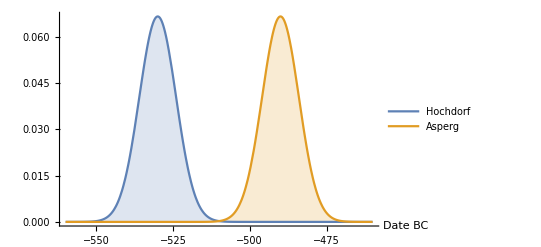

```mathematica
burialH=NormalDistribution[-530,6];
burialA=NormalDistribution[-490,6];
Plot[{
PDF[burialH,x],
PDF[burialA,x]
},{x,-560,-460},Filling->Axis,PlotLegends->{"Hochdorf","Asperg"},
Axes->{True,False},AxesLabel->{"Date BC"}
]
```

### Mothers age

```mathematica
d=NormalDistribution[0,6];
CDF[d,10.]-CDF[d,-10]
```

0.904419

#### Normal distribution

Symmetric mother distribution simply following a symmetric distribution between 15 and 45 years old:

```mathematica
mothersAgeDist=NormalDistribution[30,6];
```

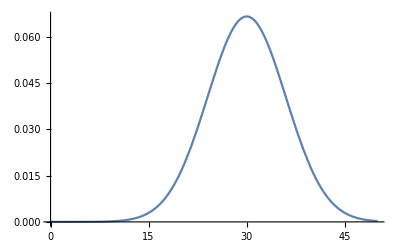

```mathematica
Plot[PDF[mothersAgeDist,x],{x,0,50}]
```

```mathematica
Quantile[mothersAgeDist,{0.005,0.995}]
```

{14.545,45.455}

```mathematica
CDF[mothersAgeDist,45]-CDF[mothersAgeDist,15.]
```

0.987581

So roughly 99% of the weight of this distribution are between 15 and 45 years

#### Generalised Gamma distribution

We can try an asymmetric case with a peak towards younger ages. Specifically, we can try to tune a generalised Gamma distribution with the following key dates:

The 0.005-Quantile should be near 15

The 0.995-Quantile should be near 45

The mean should be following empirical mothers ages, for example according to Wang, Richard J., Samer I. Al-Saffar, Jeffrey Rogers, and Matthew W. Hahn. 2023. “Human Generation Times across the Past 250,000 Years.” Science Advances 9 (1): eabm7047. -> 23.2 years

We can try things out.

```mathematica
Manipulate[
motherAgeDist2=GammaDistribution[α,β,1,μ];
Row[{
Plot[PDF[motherAgeDist2,x],{x,0,50},PlotRange->All,ImageSize->300,Filling->Axis],StringForm["Mean: `1`, 99%-range: `2`",Round[Mean[motherAgeDist2],0.01],Round[#,0.1]&/@Quantile[motherAgeDist2,{0.005,0.995}]]
}],
{{α,2},1,5},{{β,2},1,5},{μ,5,15}
]
```

OK, we get close, but how to do this systematically?

```mathematica
MinFunc[α_,β_,μ_]:=Module[{dist,q1,q2,m},
dist=GammaDistribution[α,β,1,μ];
{q1,q2}=Quantile[dist,{0.005,0.995}];
m=Mean[dist];
(q1-15)^2+(q2-45)^2+(m-23.2)^2
]
```

```mathematica
m=FindMinimum[MinFunc[α,β,μ],{{α,2},{β,3},{μ,12}}]
```

{3.20475×10^-30,{α→2.31385,β→3.81424,μ→14.3744}}

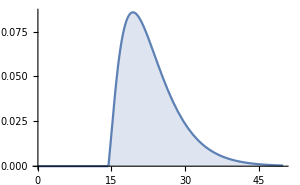
-Graphics-Mean: 23.2, 99%-range: {15.,45.}

```mathematica
motherAgeDist2=GammaDistribution[α,β,1,μ]/.m[[2]];
Row[{
Plot[PDF[motherAgeDist2,x],{x,0,50},PlotRange->All,ImageSize->300,Filling->Axis],StringForm["Mean: `1`, 99%-range: `2`",Round[Mean[motherAgeDist2],0.01],Round[#,0.1]&/@Quantile[motherAgeDist2,{0.005,0.995}]]
}]
```

Perfect!

For Stan, we need the inverse of the scale parameter, so

```mathematica
1/(β/.m[[2]])
```

0.262176

#### Other distributions

General::unfl: Underflow occurred in computation.

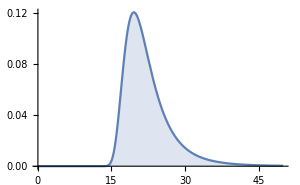
-Graphics-Mean: 22.32, 99%-range: {15.5,45.2}

```mathematica
motherAgeDist3=FrechetDistribution[6.5,20];
Row[{
Plot[PDF[motherAgeDist3,x],{x,0,50},PlotRange->All,ImageSize->300,Filling->Axis],StringForm["Mean: `1`, 99%-range: `2`",Round[Mean[motherAgeDist3],0.01],Round[#,0.1]&/@Quantile[motherAgeDist3,{0.005,0.995}]]
}]
```

```mathematica
MinFunc[α_,β_]:=Module[{dist,q1,q2,m},
dist=FrechetDistribution[α,β];
{q1,q2}=Quantile[dist,{0.005,0.995}];
m=Mean[dist];
(q1-15)^2+(q2-45)^2+(m-23.2)^2
]
```

```mathematica
m=FindMinimum[MinFunc[α,β],{{α,1.4},{β,10}}]
```

{0.962883,{α→6.57742,β→20.1739}}

## Sibling model

```mathematica
stanData=readStanDataset["model_siblings_output.csv"];
```

```mathematica
stanData
```

Dataset[<>]

```mathematica
columns=stanData[1,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,burial_h,burial_a,age_h,age_a,age_m_h,birth_date_mother,age_m_a}

```mathematica
variableNames={"burial_h","burial_a","age_h","age_a","age_m_h","age_m_a"}
```

{burial_h,burial_a,age_h,age_a,age_m_h,age_m_a}

```mathematica
priorDists={
NormalDistribution[-530,6],
NormalDistribution[-490,6],
NormalDistribution[45,6],
NormalDistribution[30,6],
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113},
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113}
};
```

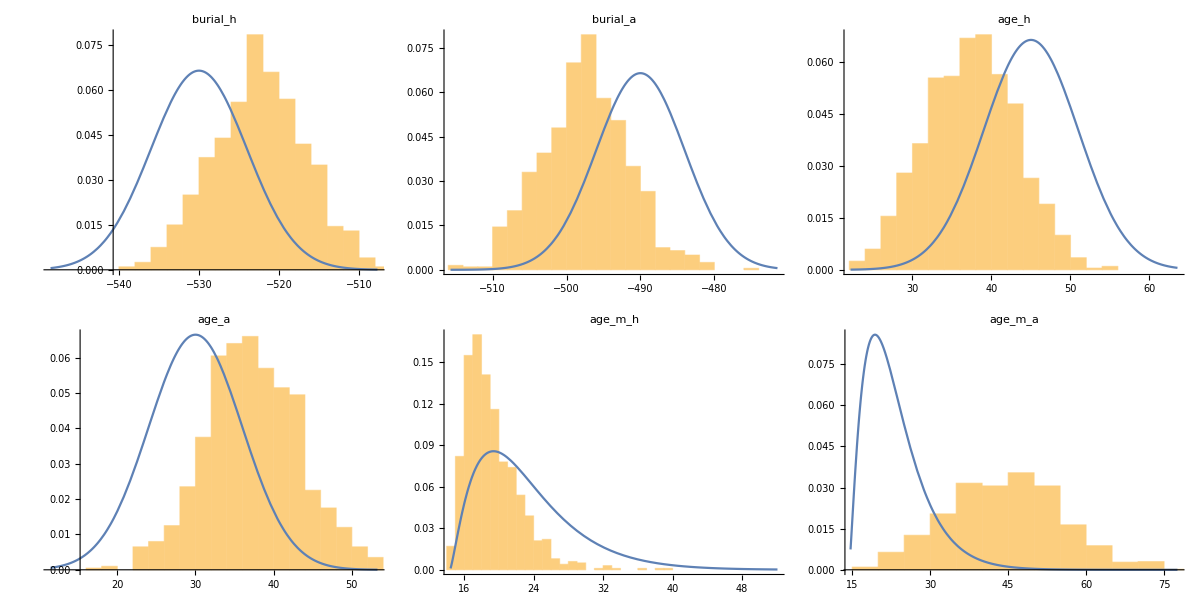

```mathematica
p=Module[
{d,pd,left,right},
Grid[
Partition[Table[
v=variableNames[[i]];
d=stanData[All,v];
pd=priorDists[[i]];
left=Min[Quantile[d,0.001],Quantile[pd,0.001]];
right=Max[Quantile[d,0.999],Quantile[pd,0.999]];
Show[
Histogram[d,Automatic,"PDF",PlotLabel->v,ImageSize->200,Axes->{True,False}],
Plot[PDF[pd,x],{x,left,right}],
PlotRangeClipping->True,PlotRange->{{left, right},All}
],
{i,Length@variableNames}
],3],Spacings->{2,2}
]
]
```

```mathematica
Export["images/"]
```

```mathematica
TableForm[Table[Quantile[stanData[All,v],#]&/@{0.05,0.5,0.95},{v,variableNames}],TableHeadings->{variableNames,{"5-Percentile","Median","95-Percentile"}}]
```

| 5-Percentile | Median | 95-Percentile
burial_h | -532.123 | -522.51 | -513.181
burial_a | -507.208 | -497.496 | -488.429
age_h | 28.1291 | 37.5346 | 46.9314
age_a | 27.4721 | 37.1521 | 47.6934
age_m_h | 15.5377 | 18.3882 | 25.0422
age_m_a | 26.3033 | 44.4688 | 62.4715

```mathematica
paramNames=variableNames[[;;5]]
```

{burial_h,burial_a,age_h,age_a,age_m_h}

```mathematica
combinedPrior=ProductDistribution@@(priorDists[[;;5]])
```

ProductDistribution[NormalDistribution[-530,6],NormalDistribution[-490,6],NormalDistribution[45,6],NormalDistribution[30,6],GammaDistribution[2.31385,3.81424,1,14.3744]]

```mathematica
logLSiblings[paramVector_]:=Module[{burialH,burialA,ageH,ageA,ageMH,ageMA,birthDateMother},
{burialH,burialA,ageH,ageA,ageMH}=paramVector;
birthDateMother=burialH-ageH-ageMH;
ageMA=burialA-ageA-birthDateMother;
LogLikelihood[combinedPrior,{paramVector}]+LogLikelihood[priorDists[[5]],{ageMA}]
]
```

```mathematica
posteriorDraws=stanData[All,paramNames/*Values]//Normal;
```

```mathematica
posteriorLogLvalues=logLSiblings/@posteriorDraws;
```

```mathematica
logMarginalLikelihood[posteriorDraws,posteriorLogLvalues,logLSiblings]
```

Estimating α as 4.9115

Estimating piHat as 0.618

-10.2048

## Avuncular model

```mathematica
stanData=readStanDataset["model_avuncular_output.csv"];
```

```mathematica
stanData
```

Dataset[<>]

```mathematica
columns=stanData[1,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,burial_h,burial_a,age_h,age_a,age_m_h,age_m_a,birth_date_grandmother,birth_date_sister,age_m_s}

```mathematica
variableNames={"burial_h","burial_a","age_h","age_a","age_m_h","age_m_s","age_m_a"}
```

{burial_h,burial_a,age_h,age_a,age_m_h,age_m_s,age_m_a}

```mathematica
priorDists={
NormalDistribution[-530,6],
NormalDistribution[-490,6],
NormalDistribution[45,6],
NormalDistribution[30,6],
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113},
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113},
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113}
};
```

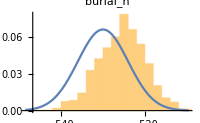
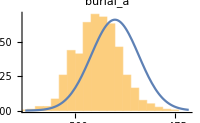
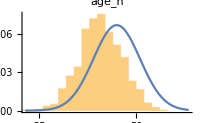
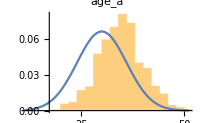
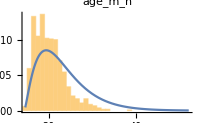
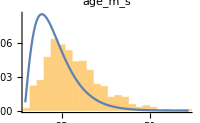
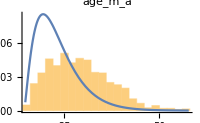

```mathematica
Module[
{d,pd,left,right},
Row[
Table[
v=variableNames[[i]];
d=stanData[All,v];
pd=priorDists[[i]];
left=Min[Quantile[d,0.001],Quantile[pd,0.001]];
right=Max[Quantile[d,0.999],Quantile[pd,0.999]];
Show[
Histogram[d,Automatic,"PDF",PlotLabel->v,ImageSize->200,Axes->{True,False}],
Plot[PDF[pd,x],{x,left,right}],
PlotRangeClipping->True,PlotRange->{{left, right},All}
],
{i,Length@variableNames}
],
Spacer[20]
]
]
```

```mathematica
TableForm[Table[Quantile[stanData[All,v],#]&/@{0.05,0.5,0.95},{v,variableNames}],TableHeadings->{variableNames,{"5-Percentile","Median","95-Percentile"}}]
```

| 5-Percentile | Median | 95-Percentile
burial_h | -535.353 | -525.112 | -516.444
burial_a | -503.171 | -494.311 | -484.999
age_h | 31.874 | 40.6298 | 50.0058
age_a | 25.6567 | 34.5588 | 43.6756
age_m_h | 15.7118 | 19.5602 | 27.166
age_m_s | 18.0852 | 27.0772 | 43.2163
age_m_a | 17.72 | 28.4617 | 43.1481

```mathematica
paramNames=variableNames[[;;6]]
```

{burial_h,burial_a,age_h,age_a,age_m_h,age_m_s}

```mathematica
combinedPrior=ProductDistribution@@(priorDists[[;;6]])
```

ProductDistribution[NormalDistribution[-530,6],NormalDistribution[-490,6],NormalDistribution[45,6],NormalDistribution[30,6],GammaDistribution[2.31385,3.81424,1,14.3744],GammaDistribution[2.31385,3.81424,1,14.3744]]

```mathematica
logLavuncular[paramVector_]:=Module[{burialH,burialA,ageH,ageA,ageMH,ageMA,ageMS,birthDateMother,birthDateSister},
{burialH,burialA,ageH,ageA,ageMH,ageMA}=paramVector;
birthDateMother=burialH-ageH-ageMH;
birthDateSister=burialA-ageA-ageMA;
ageMS=birthDateSister-birthDateMother;
LogLikelihood[combinedPrior,{paramVector}]+LogLikelihood[priorDists[[6]],{ageMS}]
]
```

```mathematica
posteriorDraws=stanData[All,paramNames/*Values]//Normal;
```

```mathematica
posteriorLogLvalues=logLavuncular/@posteriorDraws;
```

```mathematica
logMarginalLikelihood[posteriorDraws,posteriorLogLvalues,logLavuncular]
```

Estimating α as 6.77009

Estimating piHat as 0.388

-5.71911

## Cousin model

```mathematica
stanData=readStanDataset["model_cousins_output.csv"];
```

```mathematica
stanData
```

Dataset[<>]

```mathematica
columns=stanData[1,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,burial_h,burial_a,age_h,age_a,age_m_h,age_m_a,age_m2_h,birth_date_grandmother,age_m2_a}

```mathematica
variableNames={"burial_h","burial_a","age_h","age_a","age_m_h","age_m_a","age_m2_h","age_m2_a"}
```

{burial_h,burial_a,age_h,age_a,age_m_h,age_m_a,age_m2_h,age_m2_a}

```mathematica
priorDists={
NormalDistribution[-530,6],
NormalDistribution[-490,6],
NormalDistribution[45,6],
NormalDistribution[30,6],
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113},
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113},
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113},
GammaDistribution[α,β,1,μ]/.{α->2.313854479923621,β->3.8142370826527583,μ->14.374410438813113}
};
```

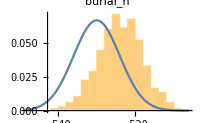
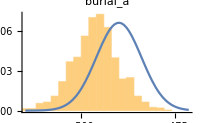
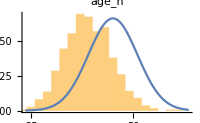
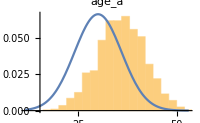
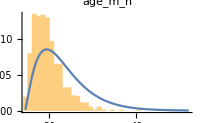
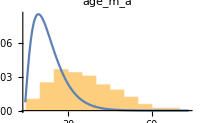
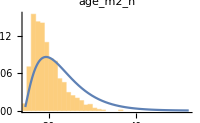
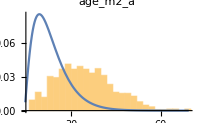

```mathematica
Module[
{d,pd,left,right},
Row[
Table[
v=variableNames[[i]];
d=stanData[All,v];
pd=priorDists[[i]];
left=Min[Quantile[d,0.001],Quantile[pd,0.001]];
right=Max[Quantile[d,0.999],Quantile[pd,0.999]];
Show[
Histogram[d,Automatic,"PDF",PlotLabel->v,ImageSize->200,Axes->{True,False}],
Plot[PDF[pd,x],{x,left,right}],
PlotRangeClipping->True,PlotRange->{{left, right},All}
],
{i,Length@variableNames}
],
Spacer[20]
]
]
```

```mathematica
TableForm[Table[Quantile[stanData[All,v],#]&/@{0.05,0.5,0.95},{v,variableNames}],TableHeadings->{variableNames,{"5-Percentile","Median","95-Percentile"}}]
```

| 5-Percentile | Median | 95-Percentile
burial_h | -533.539 | -523.881 | -514.618
burial_a | -506.109 | -496.09 | -486.209
age_h | 30.1849 | 38.8798 | 48.4907
age_a | 25.6435 | 35.9259 | 45.7069
age_m_h | 15.5028 | 18.9986 | 26.1178
age_m_a | 19.8248 | 34.0259 | 55.1282
age_m2_h | 15.6646 | 18.89 | 26.7075
age_m2_a | 19.8085 | 33.8145 | 51.7114

```mathematica
paramNames=variableNames[[;;7]]
```

{burial_h,burial_a,age_h,age_a,age_m_h,age_m_a,age_m2_h}

```mathematica
combinedPrior=ProductDistribution@@(priorDists[[;;7]])
```

ProductDistribution[NormalDistribution[-530,6],NormalDistribution[-490,6],NormalDistribution[45,6],NormalDistribution[30,6],GammaDistribution[2.31385,3.81424,1,14.3744],GammaDistribution[2.31385,3.81424,1,14.3744],GammaDistribution[2.31385,3.81424,1,14.3744]]

```mathematica
logLcousins[paramVector_]:=Module[{burialH,burialA,ageH,ageA,ageMH,ageMA,ageM2H,ageM2A,birthDateMother},
{burialH,burialA,ageH,ageA,ageMH,ageMA,ageM2H}=paramVector;
birthDateMother=burialH-ageH-ageMH-ageM2H;
ageM2A=burialA-ageA-ageMA-birthDateMother;
LogLikelihood[combinedPrior,{paramVector}]+LogLikelihood[priorDists[[7]],{ageM2A}]
]
```

```mathematica
posteriorDraws=stanData[All,paramNames/*Values]//Normal;
```

```mathematica
posteriorLogLvalues=logLcousins/@posteriorDraws;
```

```mathematica
logMarginalLikelihood[posteriorDraws,posteriorLogLvalues,logLcousins]
```

Estimating α as 8.59734

Estimating piHat as 0.222

-8.87956

## Summary

```mathematica
logMarginalLikelihoods={-10.204762497708206,-5.719108462960126,-8.879563166388571};
params={5,6,7};
```

```mathematica
relativeProbabilities=Exp[logMarginalLikelihoods-Max@logMarginalLikelihoods];
relativeProbabilities/=Total@relativeProbabilities;
bayesFactors={"n/a",relativeProbabilities[[2]]/relativeProbabilities[[3]],relativeProbabilities[[3]]/relativeProbabilities[[1]]};
```

```mathematica
TableForm[
Transpose@{params,logMarginalLikelihoods,relativeProbabilities,bayesFactors},
TableHeadings->{{"(Half-)siblings","Avuncular","(Double) First Cousins"}, {"Anzahl Parameter","Log-Evidence","Relative\nprobability","Bayes Factor over\nnext-best model"}}
]
```

| Anzahl Parameter | Log-Evidence | Relative
probability | Bayes Factor over
next-best model
(Half-)siblings | 5 | -10.2048 | 0.0106954 | n/a
Avuncular | 6 | -5.71911 | 0.949058 | 23.5813
(Double) First Cousins | 7 | -8.87956 | 0.0402462 | 3.76294

Adding genetic evidence

```mathematica
geneticProbFirstD=0.012;
geneticProbSecondD=0.988;
geneticProbFirstD+geneticProbSecondD
```

1.

```mathematica
logMarginalLikelihoods={-10.2,-10.2,-5.7,-8.88};
relativeProbabilities=Exp[logMarginalLikelihoods]*{geneticProbFirstD,geneticProbSecondD,geneticProbSecondD,geneticProbSecondD};
norm=Total[relativeProbabilities];
TableForm[
Transpose@{{1,2,2,2},logMarginalLikelihoods,relativeProbabilities/norm,relativeProbabilities/relativeProbabilities[[1]]},
TableHeadings->{{"Full siblings","Half Siblings","Avuncular","Double First Cousins"}, {"Parameters","Log-Evidence (Dating/Ages)","Full\nprobability (+genetics)","Bayes Factor over\nworst model"}}
]
```

| Parameters | Log-Evidence (Dating/Ages) | Full
probability (+genetics) | Bayes Factor over
worst model
Full siblings | 1 | -10.2 | 0.000128157 | 1.
Half Siblings | 2 | -10.2 | 0.0105516 | 82.3333
Avuncular | 2 | -5.7 | 0.949821 | 7411.41
Double First Cousins | 2 | -8.88 | 0.0394989 | 308.208

```mathematica
n
```